#### Examine the elastic map of Brown, Angel, Ross (2016) INSTRUCTIONS: Run common_funs.nb, then ES_FindSymGroups.nb, then this notebook

#### Path to text file (user will need to change this)

```mathematica
fname="C:\\Users\\Walter\\Documents\\seismology\\MomentTensor\\ConsolidatedFiles\\Brown2016_Table2.txt";
fname ="/Users/carltape/Desktop/REPOSITORIES/mtbeach/mathematica/Brown2016_Table2.txt";
```

#### Read the local text file Brown2016_Table2.txt, then compare BT2 with Brown’s Table2. Units are in GPa As stated in the Table 2 footnote, the uncertainties are 2σ

```mathematica
BT2=ReadList[fname,{{Number,Number},{Number,Number},{Number,Number},{Number,Number},{Number,Number},{Number,Number},{Number,Number},{Number,Number}}];
MatrixForm[BT2]
```

#### Example entries in the table

```mathematica
Print["The third entry of the 20th row is BT2[[20, 3]] = ",MatrixForm[BT2[[20,3]]]];
Print["Its first entry is BT2[[20, 3, 1]] = ",BT2[[20,3,1]]]
```

#### Density values from Table 1 (units g/cm3)

```mathematica
rho={2.623,2.653,2.6662,2.683,2.702,2.721,2.725,2.757};
```

#### KEY COMMAND: enter the column index to pick an elastic map (j = 1, ..., 8)

```mathematica
j=1;   (* j determines the column of BT2.  j = 1, 2,..., 8 *)
```

#### Formatting functions

```mathematica
PrintTextForJ[j_]:=Print["j = ",j,", so Brown's column heading is ",BrownColumnText[j]];
BrownColumnText[1]=SequenceForm[Style["An_0",18],", all albite"];
BrownColumnText[2]=Style["An_25",18];
BrownColumnText[3]=Style["An_37",18];
BrownColumnText[4]=Style["An_48",18];
BrownColumnText[5]=Style["An_60",18];
BrownColumnText[6]=Style["An_67",18];
BrownColumnText[7]=Style["An_78",18];
BrownColumnText[8]=SequenceForm[Style["An_96",18],", almost all anorthite"];
```

#### Display output for choice of j

```mathematica
PrintTextForJ[j]
CmatBrown=({{BT2[[1, j,1]], BT2[[7, j,1]], BT2[[8, j,1]], BT2[[14,j,1]], BT2[[10,j,1]], BT2[[15,j,1]]}, {BT2[[7, j,1]], BT2[[2, j,1]], BT2[[9, j,1]], BT2[[16,j,1]], BT2[[11,j,1]], BT2[[17,j,1]]}, {BT2[[8, j,1]], BT2[[9, j,1]], BT2[[3, j,1]], BT2[[18,j,1]], BT2[[12,j,1]], BT2[[19,j,1]]}, {BT2[[14,j,1]], BT2[[16,j,1]], BT2[[18,j,1]], BT2[[4, j,1]], BT2[[20,j,1]], BT2[[13,j,1]]}, {BT2[[10,j,1]], BT2[[11,j,1]], BT2[[12,j,1]], BT2[[20,j,1]], BT2[[5, j,1]], BT2[[21,j,1]]}, {BT2[[15,j,1]], BT2[[17,j,1]], BT2[[19,j,1]], BT2[[13,j,1]], BT2[[21,j,1]], BT2[[6, j,1]]}});
CmatUncertaintiesBrown=({{BT2[[1, j,2]], BT2[[7, j,2]], BT2[[8, j,2]], BT2[[14,j,2]], BT2[[10,j,2]], BT2[[15,j,2]]}, {BT2[[7, j,2]], BT2[[2, j,2]], BT2[[9, j,2]], BT2[[16,j,2]], BT2[[11,j,2]], BT2[[17,j,2]]}, {BT2[[8, j,2]], BT2[[9, j,2]], BT2[[3, j,2]], BT2[[18,j,2]], BT2[[12,j,2]], BT2[[19,j,2]]}, {BT2[[14,j,2]], BT2[[16,j,2]], BT2[[18,j,2]], BT2[[4, j,2]], BT2[[20,j,2]], BT2[[13,j,2]]}, {BT2[[10,j,2]], BT2[[11,j,2]], BT2[[12,j,2]], BT2[[20,j,2]], BT2[[5, j,2]], BT2[[21,j,2]]}, {BT2[[15,j,2]], BT2[[17,j,2]], BT2[[19,j,2]], BT2[[13,j,2]], BT2[[21,j,2]], BT2[[6, j,2]]}});
Tmat=TmatOfCmat[CmatBrown];
Print["Brown's Voigt matrix would be CmatBrown = ",MatrixForm[CmatBrown]];
Print["Brown's Voigt matrix uncertainties      = ",MatrixForm[CmatUncertaintiesBrown]];
Print["Our matrix would be Tmat                = ",MatrixForm[Round[Tmat,.0001]]];
Print["Density (g/cm3)                         = ",MatrixForm[rho[[j]]]];
```

```mathematica
CmatBrown==Transpose[CmatBrown]
```

#### Check for stability:

```mathematica
PrintTextForJ[j];
Eigenvalues[CmatBrown]
Eigenvalues[Tmat]
```

```mathematica
denominator=1;
```

```mathematica
WantDetails="WantDetails"
```

#### Σ = MONO

```mathematica
OutputFor[Tmat,MONO]
```

#### Expanded output

```mathematica
PrintTextForJ[j];
Print["Tmat                                              = ",MatrixForm[Round[Tmat,.01]]];
Print["Tmat for a closest (may not be unique)            = ",MatrixForm[Round[Closest[Tmat,MONO],.01]]];
Print["Cmat for a closest                                = ",MatrixForm[Round[CmatOfTmat[Closest[Tmat,MONO]],.01]]];
Print["Cmat uncertainties                                = ",MatrixForm[CmatUncertaintiesBrown]];
Print["|Cmat - Cmat for a closest|                       = ",MatrixForm[Round[Abs[CmatBrown-CmatOfTmat[Closest[Tmat,MONO]]],.1]]];
Print["Cmat uncertainties - |Cmat - Cmat for a closest| = "MatrixForm[Map[Style[#,If[#<0,Red,Black]]&,Round[CmatUncertaintiesBrown-Abs[CmatBrown-CmatOfTmat[Closest[Tmat,MONO]]],.1],{2}]]];
```

#### Σ = ORTH

```mathematica
OutputFor[Tmat,ORTH]
```

#### Σ = TET

```mathematica
OutputFor[Tmat,TET]
```

#### Σ = CUBE

```mathematica
OutputFor[Tmat,CUBE]
```

#### Σ = TRIG

```mathematica
OutputFor[Tmat,TRIG]
```

#### Σ = XISO

```mathematica
OutputFor[Tmat,XISO]
```

#### Σ = ISO

```mathematica
OutputFor[Tmat,ISO]
```

#### Display lattice with beta angles

```mathematica
PrintTextForJ[j];
LatticeOfDTs[Tmat]
Print["[T] = ",1/denominator,MatrixForm[denominator Tmat]]
```

#### From the lattice and the appropriate U you get the symmetry group of T. See Theorem 3of TapeTape2022.

#### To get the result for Brown’s other 7 columns, change j and re-run.

## Lattice diagrams for reference:

j = 1, so Brown's column heading is An_0, all albite

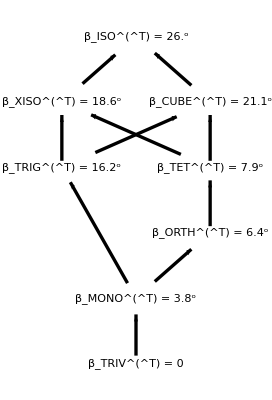

j = 2, so Brown's column heading is An_25

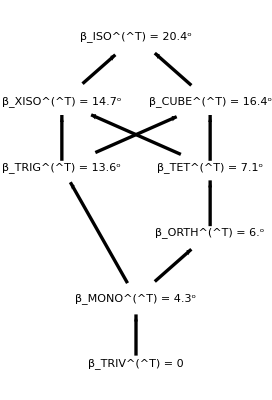

j = 3, so Brown's column heading is An_37

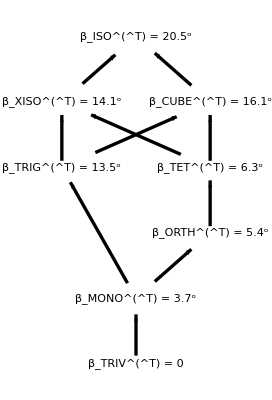

j = 4, so Brown's column heading is An_48

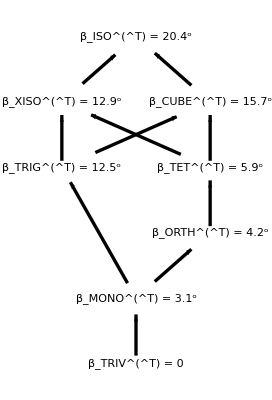

j = 5, so Brown's column heading is An_60

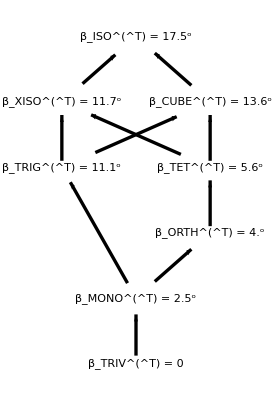

j = 6, so Brown's column heading is An_67

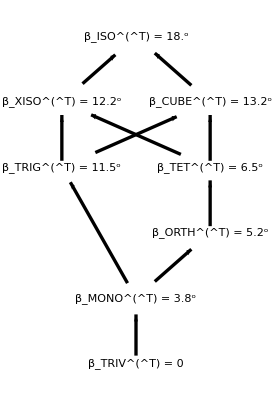

j = 7, so Brown's column heading is An_78

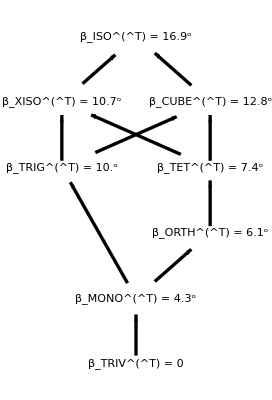

j = 8, so Brown's column heading is An_96, almost all anorthite